```mathematica
Subscript[N, 2]={{370.0*^-9,23.698*^-31},{405.8*^-9,16.146*^-31},{532.2*^-9,5.302*^-31},{660.0*^-9,2.988*^-31}};
Subscript[O, 2]={{370.0*^-9,21.269*^-31},{405.8*^-9,14.373*^-31},{532.2*^-9,4.740*^-31},{660.0*^-9,1.935*^-31}};
Ar={{370.0*^-9,20.361*^-31},{405.8*^-9,13.881*^-31},{532.2*^-9,4.563*^-31},{660.0*^-9,1.91*^-31}};
```

```mathematica
FindFit[Subscript[N, 2],a/λ^4,a,λ]
```

{a→4.42299×10^-56}

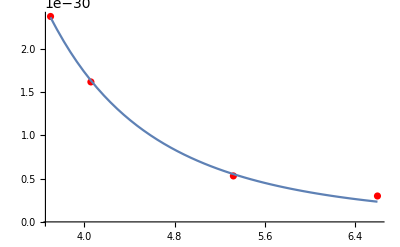

```mathematica
Show[ListPlot[Subscript[N, 2],PlotStyle->Red],Plot[a/λ^4/.{a->4.422986577540245*^-56},{λ,3.7*^-7,6.6*^-7}]]
```

```mathematica
FindFit[Subscript[O, 2],a/λ^4,a,λ]
```

{a→3.95023×10^-56}

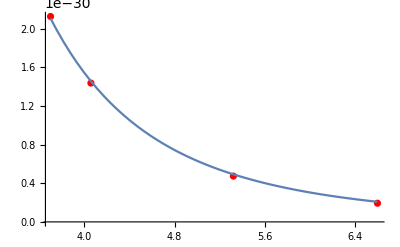

```mathematica
Show[ListPlot[Subscript[O, 2],PlotStyle->Red],Plot[a/λ^4/.{a->3.950229946366524*^-56},{λ,3.7*^-7,6.6*^-7}]]
```

```mathematica
FindFit[Ar,a/λ^4,a,λ]
```

{a→3.79322×10^-56}

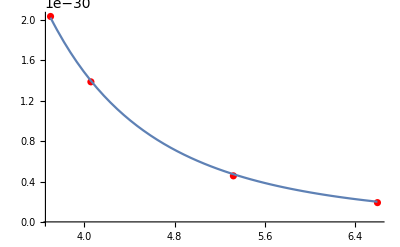

```mathematica
Show[ListPlot[Ar,PlotStyle->Red],Plot[a/λ^4/.{a->3.7932158797866264*^-56},{λ,3.7*^-7,6.6*^-7}]]
```